(-3823.79-271.5 Log[0.000071442 y])/Log[0.000071442 y]

(-3821.81-227.1 Log[0.0000318408 (1.-1. y)])/Log[0.0000318408 (1.-1. y)]

0.623626

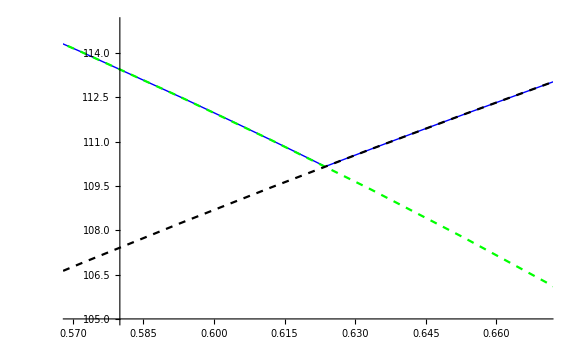

```mathematica
psat1[T_]=10^(4.72583-1660.652/(T+271.5));
psat2[T_]=10^(5.0768-1659.793/(T+227.1));
P=3.8;
t=Round[T/.FindRoot[psat1[T]/P==1-psat2[T]/P,{T,0}]];
xt=psat1[t]/P;
xt2=N[Round[100*psat1[t]/P]/100];

temp1[y_]=Quiet[T/.Solve[psat1[T]/P==y,T][[1]]]
temp2[y_]=Quiet[T/.Solve[1-psat2[T]/P==y,T][[1]]]

int=Y/.FindRoot[temp1[Y]==temp2[Y],{Y,0.2}]


f[y_]=Piecewise[{{temp2[y],0≤y≤int},{temp1[y],int<y≤1}}];

Plot[{f[y],temp2[y],temp1[y]},{y,0,1},PlotStyle->{{Thick,Blue},{Dashed,Green},{Dashed,Black}},PlotRange->{{xt2-0.05,xt2+0.05},{t-5,t+5}},ImageSize->Large]
```

```mathematica
3
```

```mathematica
0.0889*2
```

0.1778